This notebook is Copyright ©, 2008 Scientific Arts, LLC,  all rights reserved.  It may be redistributed only in full and in its original form without modification; and it may not be used for any commercial purpose without permission from Scientific Arts.  A non-exclusive royalty-free license is given to reproduce and use all the of the Mathematica code in this notebook for any purpose whatsoever, as well as any of the ideas.   No guarantee whatsoever is given as to the  accuracy or functionality of anything presented in this document.  Use at your own risk. 

Enjoy: I hope that it's useful. For further information on  A WorkLife FrameWork, please click on the Scientific Arts banner above.

Version of Tue 15 Apr 2008 13:20:00

Go to http://www.scientificarts.com/worklife/notebooks/ for updates to this notebook

## The Structure of Documentation Directories

Typically when you have an application such as a package in a directory that directory will contain the documentation for that application.

Let us say that your application is in a directory called MyApplication.  Then, within this directory, there will be a directory called Documentation and there will also be a file called PacletInfo.m.  More about the PacletInfo.m file will be described later on.

Within the Documentation directory there will be another directory called English (assuming that your documentation is in English).  And within the English directory will be three directories called

Guides

Tutorials

ReferencePages

And within the ReferencePages directory is another directory called Symbols.

So the form of the directory hierarchy looks like:

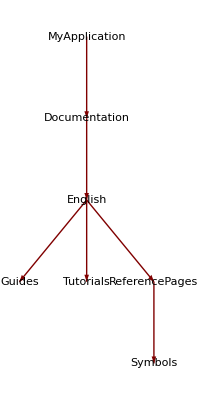

The three directories, Guides, Tutorials, and ReferencePages have the following purposes:

#### Guides

This is the directory in which, for example, Tables of Contents notebooks would reside.  Also, more generally, Guide Pages would go here.

#### Tutorials

Here go the actual tutorials: the discursive content that you create.  In effect this is the descriptive documentation itself.

#### ReferencePages

In this directory there is a subdirectory called Symbols.  In the Symbols directory is placed the notebooks—one for each function—that give the specific documentation for each function in your package.  At the very least each such page would contain the usage message for each function in your package.

### The PacletInfo.m File

As mentioned above, within the package directory which we are calling MyApplication there will also be a file called PacletInfo.m.  This is a file with a specific structure which tells Mathematica what is contained within the Guides, Tutorials, and ReferencePages directories and how the Documentation Center should categorize and access them.  The PacletInfo.m file is a plain text file with elements that describe what sorts of materials are contained in the  Guides, Tutorials, and ReferencePages directories as well as things such as what Context the functions described within the ReferencePages belong to.  Also it lets the Documentation Center know how to list the material on the Installed Add-Ons page that is linked to from the front page of the Documentation Center.

## Internal Details

A very bare bones approach to creating Documentation Center material would make use of the directory structure described above along with a hand coded PacletInfo.m file.  In A WorkLife FrameWork all of this is created automatically, but it is useful to know some of this information in case one wants to modify documentation directly as well as for potential debugging purposes.

In addition to the PacletInfo.m file the notebooks that will be placed within the Guides, Tutorials, and ReferencePages directories must be modified in a particular way which is described below.

### PacletInfo.m file

Here is how a PacletInfo.m file might be built.  We will describe a simple case where there is one Guide page, one Tutorial, and one function Reference page.  Assume that

The Guide page is a notebook called TableOfContents.nb, this will contain links to each of the Tutorial pages.

The Tutorial pages comprise two notebooks called ATutorial.nb and AnotherTutorial.nb

The Reference pages comprise two notebooks called AFunction.nb and AnotherFunction.nb

Note that, in the case of the Reference page's name, it generally should correspond to the function's name itself.   So we assume that the package that is being documented has a function called AFunction.

Now further assume that the package Context is MyApplication`MyPackage`.  This assumes that the package's file is called MyPackage.m and is within the directory called MyApplication.  The PacletInfo.m file is also in this directory as we mentioned earlier.

So, with all of this, the directory and file structure is

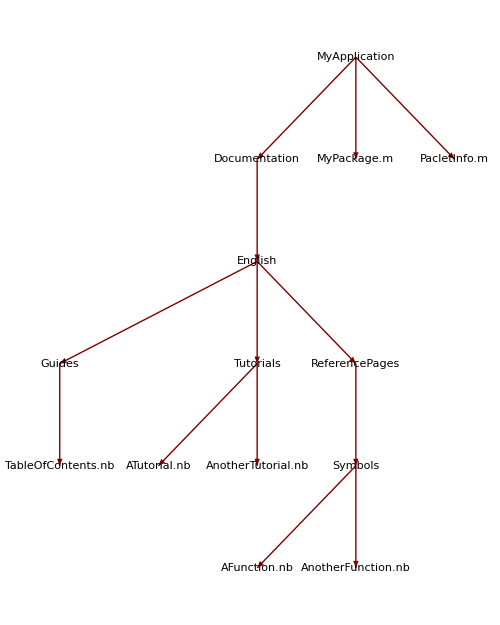

Finally, assume that you want the Documentation Center to list your package by a name that may be different from its Context name, say "My Magnificent Package".  Note that this can contain spaces, but other items that we specify should not contain spaces—just to be safe. And also assume that you want the root of hyperlinks that lead to it to be called FirstApplication.  We are just using FirstApplication here to show the generality that is possible.  It might make much more sense to call it MyApplication or MyPackage for clarity. Indeed you would want this to be a word that, when it is typed into the input field of the Documentation Center toolbar, would be the one that you expect to lead you to a table of contents.  So, the package name might be the best choice.

Here is the content of the PacletInfo.m file that would represent this overall circumstance.  Note that there is also a specification of the packages current Version number.  This is not mandatory, but it makes sense to include it.

Paclet[
 
 	Name -> "My Magnificent Package",
 
 	Version -> "1.1.0",
 
 	Extensions -> {
   		{"Application", Root -> "FirstApplication", Context -> "MyApplication`MyPackage`"},
   			{"Documentation", 
   			   Language -> "English", 
   			   LinkBase -> "FirstApplication", 
    			Resources -> {
      				"Guides/TableOfContents"}
    			},
   			{"Documentation", 
   			   Language -> "English", 
   			   LinkBase -> "FirstApplication", 
    			Resources -> {
      				"Tutorials/ATutorial",
      				"Tutorials/AnotherTutorial"
      				}
    			},
   			{"Documentation", 
   			   Language -> "English", 
   			   LinkBase -> "FirstApplication", 
    			Resources -> {
      				"ReferencePages/Symbols/AFunction",
      				"ReferencePages/Symbols/AnotherFunction"
      			}
    	}
   }
 ]

### Preparing the Notebooks

The simplest way to prepare the notebooks that you will place in the Guides, Tutorials, and ReferencePages directories is to make sure that they have several key properties.  In general you will want to create these notebooks and then make the changes that we describe in the following in duplicates of the notebooks rather than the originals.

However the first item can, and probably should, be done to the originals.

#### First Step

For each notebook call its notebook object nb.  Then execute the following for each notebook in turn:

```mathematica
SetOptions[nb,System`CreateCellID->True];
```

Of course, alternatively, you could execute the following within the notebook itself and then delete it:

```mathematica
SetOptions[EvaluationNotebook[],System`CreateCellID->True];
```

Once this has been done you should select the entire notebook's contents, copy it, then select the entire notebook's contents again, and past it back.  Alternatively, and much more easily, you can do this programmatically as follows:

```mathematica
Module[{nbg},

nbg=NotebookGet[nb];

NotebookPut[nbg,nb]
];
```

Or, you can perform both steps using the following—again assuming that you have assigned the notebook's NotebookObject to the parameter nb.  Here some more code is inserted to make sure that the notebook in question allows for its cells to be modified and so on:

```mathematica
Module[{nbg,editable},

editable=Editable/.Options[nb,Editable];

SetOptions[nb,Editable->True];

SetOptions[nb,System`CreateCellID->True];

nbg=NotebookGet[nb];

SelectionMove[nb,All,Notebook];
SetOptions[NotebookSelection[nb],Editable->True,Deletable->True,Copyable->True];

NotebookPut[nbg,nb];

SetOptions[nb,Editable->editable]

];
```

#### Second Step

Each of the notebooks should be assigned the Wolfram/Reference.nb style sheet.  This is not absolutely necessary, but making this assignment will bring the style of your notebooks into alignment with those already in the Documentation Center.  (See below if you do not wish to do this.)

An important thing to note is that the Wolfram/Reference.nb style sheet generally does not allow editing of the notebook that it is assigned to.  So you should only make this change to the final notebook that you will be using, after you have made all final edits to it.

To make this style sheet assignment execute the following

```mathematica
SetOptions[nb,StyleDefinitions->FrontEnd`FileName[{"Wolfram"},"Reference.nb"]]
```

When you do this you will notice that the notebook automatically acquires the Documentation Center toolbar.

If, on the other hand, you don't want to use the Wolfram/Reference.nb style sheet, you can still use your notebooks with whatever style sheet you wish—this way you can retain whatever appearance you want to maintain, as well as any custom style definitions you chose to add.

The one change that you will need to make though is to add the Documentation Center Toolbar.  To do this you simply execute the following for the notebook object nb.

```mathematica
SetOptions[nb,DockedCells->FEPrivate`FrontEndResource["FEExpressions","HelpViewerToolbar"]]
```

#### Third Step

When a notebook is assigned the  Wolfram/Reference.nb style sheet it will automatically have headers and footers that, when it is printed out, will state that the notebook was printed from the Documentation Center and that Wolfram Research owns the copyright to its content.  Of course this is not the right thing to do for non-Wolfram documentation Center pages, so you will probably want to change these as well for your various notebooks.  The simplest thing to do is to modify all of your notebooks' headers and footers to :

```mathematica
SetOptions[nb,
PageFooters->{{None,None,None},{Cell[TextData[{"© 2008 [[***YOUR NAME OR COMPANY HERE***]]. All rights reserved."}],"PageFooter"],None,None}},

PageHeaders->{{None,None,None},{None,None,Cell[TextData[{Cell[TextData[{"Printed from [[YOUR APPLICATION'S NAME]] documentation "}],"PageHeader"],Cell[TextData[{CounterBox["Page"]}],"PageNumber"]}],CellMargins->{{Inherited,-29},{Inherited,Inherited}}]}}
]
```

#### Fourth Step

The third step is to create and prepare the TableOfContents.nb notebook.  This will have two links: one to the first Tutorial, ATutorial.nb, and another to the second Tutorial, AnotherTutorial.nb.

Here is the Cell expression for the first Cell

```mathematica
Cell[TextData[ButtonBox["A heading for the first tutorial",BaseStyle->"Link",ButtonData->"paclet:FirstApplication/tutorial/ATutorial"]],"TOCChapter",ShowGroupOpener->True]
```

And here is the Cell expression for the second cell in the table of contents

```mathematica
Cell[TextData[ButtonBox["A heading for the second tutorial",BaseStyle->"Link",ButtonData->"paclet:FirstApplication/tutorial/AnotherTutorial"]],"TOCChapter",ShowGroupOpener->True]
```

Note that you can create cells that link directly to particular locations in a Tutorial by pointing the link to the particular CellID (this is one of the reasons for Step 1 above.  Simply go to that cell in the Tutorial and examine its Cell expression using the menu command: Cell ⊳ Show Expression.  In the cell expression you will see a Cell Option of the form CellID->an integer.  Say that that integer is 123456.  Then you can create a cell in the Table of Contents that has a link to that cell in the Tutorial with the following, for example:

```mathematica
Cell[TextData[ButtonBox["A heading for the second tutorial",BaseStyle->"Link",ButtonData->"paclet:FirstApplication/tutorial/AnotherTutorial#123456."]],"TOCSection",ShowGroupOpener->True]
```

So with these you could create the notebook TableOfContents.nb programmatically as follows

```mathematica
NotebookPut[
Notebook[{ 
Cell["Table of Contents for MyApplication","TOCDocumentTitle",ShowGroupOpener->False,TextAlignment->Center],


Cell[TextData[ButtonBox["A heading for the first tutorial",BaseStyle->"Link",ButtonData->"paclet:FirstApplication/tutorial/ATutorial"]],"TOCChapter",ShowGroupOpener->True],

Cell[TextData[ButtonBox["A heading for the second tutorial",BaseStyle->"Link",ButtonData->"paclet:FirstApplication/tutorial/AnotherTutorial"]],"TOCChapter",ShowGroupOpener->True],

Cell[TextData[ButtonBox["A heading for the second tutorial",BaseStyle->"Link",ButtonData->"paclet:FirstApplication/tutorial/AnotherTutorial#123456."]],"TOCSection",ShowGroupOpener->True]},

StyleDefinitions->FrontEnd`FileName[{"Wolfram"},"Reference.nb"]
]
];
```

Then once you have created this you should save it as the notebook TableOfContents.nb.

### Placing the Notebooks

The full directory structure of your package (i.e.,  the full directory that we have called MyApplication in this document) needs to now be placed where Mathematica can find it.  Generally this will be in one of the following locations

```mathematica
ToFileName[{$UserBaseDirectory,"Applications"}]
```

```mathematica
ToFileName[{$BaseDirectory,"Applications"}]
```

The first location will allow Mathematica to find the application (and its documentation) for the particular user that is logged in.  The second location will allow system-wide access for all users who have access to that computer independent of their log-in credentials.

The easiest way to place the package in one of these locations is to do it programmatically.

So if the full path to the directory where your application is located is called fullPathToMyApplication then you can simply execute the following (this is for the first "Applications" directory above):

```mathematica
Quiet@DeleteDirectory[ToFileName[{$UserBaseDirectory,"Applications","MyApplication"}],DeleteContents->True];

CopyDirectory[fullPathToMyApplication,ToFileName[{$UserBaseDirectory,"Applications","MyApplication"}]]
```

#### Letting Mathematica Know

Once you place the completed application in one of these locations you can then either restart Mathematica or execute the following after closing the Documentation Center if it is open.

```mathematica
PacletManager`RestartPacletManager[]
```

This will generally reset much of what is needed to make Mathematica recognize the changes for the purposes of the Documentation Center.  However, the foolproof method is, of course, to restart Mathematica.